# Envariabelanalys Projekt: Stoppa tjuven!

## MA2001 Envariabelanalys HT18

Rapportversion 1, inlämnad 2019 - 01 - 06

## Team 9

André Frisk

Linnéa Olsson

## Uppgifter

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Swedish";
```

### 1a)

#### Problem

Bestäm spänningen u_C över kondensatorn och strömmen i genom resistorn vid tiden t.

#### Lösning

Följande formler används till grafen för att få ut spänningen samt strömmen:

U = U_0ⅇ^(-t/RC)
I = U/R = (251.707*e^(-t/0.6541333777642083))/(20*10^9)

#### Mathematicakod

{a→251.707,b→0.654133}

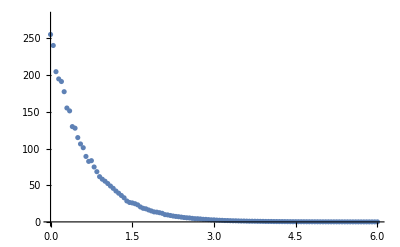

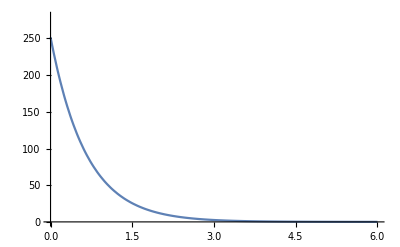

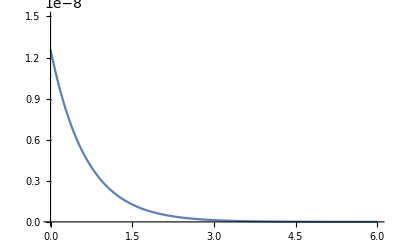

```mathematica
Remove["Global`*"]
V = Import["http://dixon.hh.se/mikael/teaching/analys/project/matserie.dat"];
cFind = FindFit[V, a*ⅇ^(-t/b), {a,b}, t]
ListPlot[V, PlotRange->{0,280}]
Plot[a*ⅇ^(-t/b) /. cFind, {t, 0, 6}, PlotRange -> {0, 280}]
Plot[(a*ⅇ^(-t/b))/(20*10^9) /. cFind, {t, 0, 6}, PlotRange -> {0, 15*10^-9}]
```

#### Slutsatser och resultat

Spänningen u_C är: 251.707 V
Strömmen i är:  Okänd

### 1b)

#### Problem

Bestäm kondensatorns kapacitans C_0.

#### Lösning

I 1a) skrev vi om så att b = RC_0. C_0 är kapacitansen och för att få ut värdet behöver vi enbart dividera med R på b.

#### Mathematicakod

```mathematica
0.6541333777642083 / (20 * 10^9)
```

3.27067×10^-11

#### Slutsats och resultat

Kondensatorns kapacitans är: C_0 = 3.27067×10^-11 F

### 1c)

#### Problem

Den tid t_1 det tar innan kondensatorns laddning minskat till hälften.

#### Lösning

Använd formeln U(t) = U_0ⅇ^(-t/b) och förläng med C_0 på båda leden, då får vi ut C_0*U = Q_0 istället. Alltså formeln:
Q_0 = Q_0ⅇ^(-t/b). Då laddningen ska va hälften för att få ut t_1 så delar vi hela formeln med 2:
Q_0/(2 Q_0) = (Q_0 ⅇ^(-t/b))/2.  Multiplicera med 2 och Q_0 på båda leden för att förenkla formeln, VL Q_0 tar ut varandra:
1/2= ⅇ^(-t/b). Ta logaritmen på båda leden för att få bort ⅇ:
Log[1/2]= -t/b. Bryt ut t på HL och täljaren blir då -1, då blir HL -1/RC_0vilket i föregående uppgifter är variabeln b. För över variabel b till VL så t blir ensam på HL. Formeln blir följande:
-Log[1/2] * b = t_1.

#### Mathematicakod

```mathematica
-Log[1/2] * 0.6541333777642083
```

0.453411

#### Slutsatser och resultat

De tar c:a 0,45 sekunder tills kondensatorns laddning minskat till hälften.

### 1d)

#### Problem

Bestäm effektutvecklingen i resistorn vid tiden t.

#### Lösning

Formeln för effekt är P = U*I men då I är okänd använder vi ström formeln I = U/R och sätter in den i effektformeln. Då får man ut:
P = U * U/R = U^2/R.

#### Mathematicakod

```mathematica
P = (((251.7065370141519*ⅇ^(-t/0.6541333777642083))^2)/(20*10^9))
```

3.16781×10^-6 ⅇ^(-3.05748 t)

```mathematica
3.1678090387828316*^-6 ⅇ^(-3.0574804282819037 t)
```

3.16781×10^-6 ⅇ^(-3.05748 t)

#### Slutsats och resultat

Effekten blir 3.1678090387828316*10^-6 *ⅇ^(-3.0574804282819037*t)

### 1e)

#### Problem

Bestäm värmeenergin som utvecklats i resistorn under tiden t_1 s och totala värmeenergin som utvecklats
då kondensatorn urladdats helt. Använd resultatet i (d).

#### Lösning

Här ska effekten användas med hjälp av en integral inom intervallet t_1 och 0:
∫_0^t_1 P(t)ⅆt = ∫_0^0.453411 3.1678090387828316*10^-6 *ⅇ^(-3.0574804282819037*t) ⅆt

#### Mathematicakod

```mathematica
Integrate[3.1678090387828316*10^-6 *ⅇ^(-3.0574804282819037*t), {t, 0, 0.453411}]
```

7.77064×10^-7

#### Slutsats och resultat

Värmeenergin är 7.77064×10^-7.

### 2a)

#### Problem

Förklara hur seriekretsen kan fungera som ett tjuvlarm.

#### Lösning/slutsats

Kapacitansen ökar då tjuvhanden närmar sig kondensatorn. Då börjar en ström flöda i kretsen och en energi kan lagras. Kondensatorn kommer inte kunna komma upp i den ampere som behövs för att larmet ska börja tjuta om det körs på egen hand, dock om något närmar sig som t.ex. tjuvens hand så ökar kapacitansen och med rätt resistans få amperemetern att uppnå 1,00µA så att sirenen kan tjuta om något är i närheten.

### 2b)

#### Problem

Bestäm de värden på serieresistansen som uppfyller specifikationerna ovan.

#### Lösning

Under labbinstruktionen finner man massa formler som ska användas här. Dessa används för att skriva om till en differentialekvation som ska lösa ut resistanserna.
E = Ri + q/c, där formel 2 vilket är: i(t) = g’(t) = C_0u'_c(t) används i formel 1. Då enligt formel 2 att i(t) = g’(t) kan man byta ut variabeln i från formel 1 till g’(t):
E = Rg’(t) + q/c. Divideras båda leden med R:
e/r = g’(t) + q/rc. Detta är nu differentialekvationen som skapats (variablerna ändrades till små bokstäver då det skapade problem i uträkningen med större bokstäver)
och som ska användas med hjälp av DSolve och D för att få ut de två resistanserna. I Mathematicakod finner du uträkningarna. Hur variabeln c får sitt värde är att ta 
c_0 och multiplicerar med 1,1 då enligt uppgiften förändras kapacitansen med minst 10%, vi räknar med det lägsta möjliga värde för c här.

#### Mathematicakod

```mathematica
Remove["Global`*"];
Diff = DSolve[{q'[t] + q[t]/(r*c)== e/r, q[0] == Subscript[c, 0] * e}, q[t], t]
D[Diff, t]
e = 250;
t = 250*10^-6;
c = 3.597733577703145*10^-11;
Subscript[c, 0] = 3.2706668888210417*10^-11;
Solve[e/r-(e*ⅇ^(-t/(c*r)) (-c+c*ⅇ^(t/(c*r))+Subscript[c, 0]))/(c*r)== 1*10^-6]
```

{{q[t]→e ⅇ^(-t/(c r)) (-c+c ⅇ^(t/(c r))+c_0)}}

{{q'[t]→e/r-(e ⅇ^(-t/(c r)) (-c+c ⅇ^(t/(c r))+c_0))/(c r)}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→3.99964×10^6},{r→1.3671×10^7}}

#### Slutsats och resultat

Resistanserna sökta för ekvationen är:
R1 = 3.99964×10^6 Ω
R2 = 1.3671×10^7 Ω

### 2c)

#### Problem

Förklara vad som händer om man väljer för stor respektive för liten resistans.

#### Lösning/slutsats

En för stor resistans gör att amperenivån inte kommer uppfyllas. En för liten resistans innebär att amperenivån uppnås men kondensatorn laddar klart för snabbt och tidskravet uppfylls inte.

### 3a)

#### Problem

Hur små kapacitansförändringar kan man mäta med ovanstående utrustning?

#### Lösning

Genom att använda sig av FindMaximum och FindRoot går det att lösa uppgiften. FindMaximum hittar lokala maximipunkter. FindRoot söker den numeriska roten. Först räknas rmax ut sedan med hjälp av funktionen solve räknas det ut och formuleras om till procent form hur små kapacitansförändringar man kan mäta. i detta fallet kommer kf att representera kapacitansförändringar.

#### Mathematicakod

```mathematica
Remove["Global`*"];
Text["a)"]
t= 250*10^-6;
Subscript[c, 0]= 3.2706668888210417*10^-11;
Subscript[q, 0] = 8.17667*10^-9;
Subscript[r, max] = 1.3671*10^7;
Subscript[r, min] = 3.99964 *10^6;


r=FindMaximum[(0.1*Subscript[q, 0]*ⅇ^(-t/(r*Subscript[c, 0])))/(r*Subscript[c, 0]),{r,Subscript[r, min],Subscript[r, max]}][[2]][[1]][[2]];

Solve[(kf*Subscript[q, 0]*ⅇ^(-t/(r*Subscript[c, 0])))/(r*Subscript[c, 0])==1*10^-6,kf][[1]][[1]][[2]]*100"%"
```

a)

8.31128 %

### Slutsats och resultat

8,31128&

### 3b)

#### Problem

Vilken spänning krävs om larmet ska kunna detektera kapacitansförändringar ner till 5% ?

#### Lösning

Förändringar ner till och med 5% skriver vi då som 0.05. Spänningen som krävs räknas ut med metoden solve och s i detta fallet kommer att representera spänningen.

#### Mathematicakod

```mathematica
Text["b)"]
changee=0.05;
r=7.948819155299942*10^6;
c=3.597733577703145*10^-11;

Solve[(changee*ⅇ^((-250*10^-6)/(r*c))*s*c)/(r*c)==10^-6,s]
```

b)

{{s→381.058}}

#### Slutsats och resultat

381V med förändring ner till och med 5%.

## Referenser

[1] Projektuppgift 1.5 hp,  http://dixon.hh.se/mikael/teaching/analys/project.shtml

[2] J. Månsson och P. Nordbeck, Endimensionell analys, Studentlitteratur (2011)

[3] Wikipedia, Capacitor, https://en.wikipedia.org/wiki/Capacitor